```mathematica
RandomGoodRule[K_:2, R_:1]:=(
rca=ResourceFunction["RandomCellularAutomatonRule"];

GoodRuleCondition[rule_]:=If[Length[Last[CellularAutomaton[rule, {RandomInteger[K-1, 100], 0}, 100]]]>150, False, With[{l=Table[Length[StripZeros[CellularAutomaton[rule, {RandomInteger[K-1, 100], 0}, {{{100}}}]]], 10]}, Mean[l]<100&&Min[l]==0&&Max[l]<150&&Max[l]>0]];

ParallelTry[If[GoodRuleCondition[#], #, $Failed]&,ParallelTable[{rca[{K, R}, "Quiescent"->True, "Type"->"Symmetric"]["RuleNumber"], K, R}, 10000]]
);

RandomGoodTotalisticRule[K_:2, R_:1]:=(
rca=ResourceFunction["RandomCellularAutomatonRule"];

GoodRuleCondition[rule_]:=If[Length[Last[CellularAutomaton[rule, {RandomInteger[K-1, 100], 0}, 100]]]>150, False, With[{l=Table[Length[StripZeros[CellularAutomaton[rule, {RandomInteger[K-1, 100], 0}, {{{100}}}]]], 10]}, Mean[l]<100&&Min[l]==0&&Max[l]<150&&Max[l]>0]];

ParallelTry[If[GoodRuleCondition[#], #, $Failed]&,ParallelTable[{rca[{K, R}, "Quiescent"->True, "Type"->"Totalistic"]["TotalisticCode"], {K, 1}, R}, 10000]]
);
```

```mathematica
rule={20, {2, 1}, 2};
rule={1329, {3, 1}, 1};
rule={123213344, 4, 2}; 
(* rule={1802174068386, 3};  *)
(* rule={52, {2, 1},2};


rule={20, {2, 1}, 2}; *)
rule={1329, {3, 1}, 1};
(* rule={52, {2, 1},2}; *)
rule={1326, {3, 1}, 1};

rule={7492516167169308646368004455659429445327030305892293894816880501426633766203150235235080168693170352598475183825783,3,2};
(* rule=RandomGoodTotalisticRule[3, 2] *)
```

```mathematica
rule={136410,{3,1},2};
rule={20, {2, 1}, 2}
```

{20,{2,1},2}

```mathematica
helperFile=Import[NotebookDirectory[]<>"kernels/helper.cl"];
templateFile=Import[NotebookDirectory[]<>"kernels/template_v"<>ToString[version]<>".cl", "Text"];
filledTemplateFile=templateFile;
```

```mathematica
TemplateReplace[rule_]:=(filledTemplateFile=StringReplace[filledTemplateFile,rule];)
```

```mathematica
Clear[StrongAssert]
StrongAssert[test_, messages__]:=If[!test, Print[messages]; Quit[4]]
SetAttributes[StrongAssert, HoldRest]
```

```mathematica
Clear[f]
f[formatString_String, args___]:=Module[{str=formatString, arglist={args}},
Do[str=StringReplace[str, "``"->ToString[arglist[[i]]],1], {i, Length[arglist]}]; str]

Clear[StringJoinTable]
StringJoinTable[args___]:=StringJoin[Table[args]]
SetAttributes[StringJoinTable, HoldAll]
```

```mathematica
PointApplyRule[rule_,init_]:=CellularAutomaton[rule, init, 1][[2,(Length[init]+1)/2]]

Clear[AnalyzeRule];
AnalyzeRule[{n_, k_, r_}]:=AnalyzeRule[{n, k, r}]=Module[{rule={n,k, r}},<|
"Rule"->rule, (* may be overrided by a totalistic rule *)
"NormalRule"->rule,  (* always {booleanfunctionnumber, colors, radius} *)
"Colors"->k,
"Radius"->r,
"Totalistic"->False,
"Number"->n,
"Quiescent"->Not[Positive[PointApplyRule[rule, ConstantArray[0, 2r+1]]]],
"Symmetric"->AllTrue[Tuples[Range[0, k-1], 2r+1], PointApplyRule[rule, #]==PointApplyRule[rule, Reverse[#]]&]
|>]

AnalyzeRule[{n_, {k_, 1}, r_}]:=AnalyzeRule[{n, {k, 1}, r}]=With[
{rule={n, {k, 1}, r}},{num=FromDigits[Reverse[PointApplyRule[rule, #]&/@Tuples[Range[0, k-1], 2r+1]], k]},
Join[AnalyzeRule[{num, k, r}],<|"Rule"->rule, "Totalistic"->True|>]
]
AnalyzeRule[{n_, k_}]:=AnalyzeRule[{n, k, 1}]
AnalyzeRule[{n_}]:=AnalyzeRule[{n, 2}]
AnalyzeRule[n_]:=AnalyzeRule[{n}]
```

```mathematica
ar=AnalyzeRule[rule]

n=ar["Number"];
k=ar["Colors"];
r=ar["Radius"];

ArrayPlot[CellularAutomaton[{n, k, r}, {RandomInteger[k-1, 100], 0}, 300], ImageSize->Small]
```

<|Rule→{20,{2,1},2},NormalRule→{1771476584,2,2},Colors→2,Radius→2,Totalistic→True,Number→1771476584,Quiescent→True,Symmetric→True|>

-Graphics-

```mathematica
StrongAssert[ar["Quiescent"], "Rule Not Quiescent"]
```

```mathematica
Clear[XorList]
XorList[inp__]:=Xor@@@Transpose[{inp}]
```

```mathematica
UpperHalf[list_List]:=list[[;;(Length[list]/2)]]
LowerHalf[list_List]:=list[[(Length[list]/2+1);;]]

Clear[ShannonForm]
ShannonForm[fmap_List]:=Module[{index, upper, lower, upperExpr, lowerExpr, outputExpr},
index=Log2[Length[fmap]];

If[index<=0, Return[First[fmap]]];

upper=fmap[[1;;;;2]];
lower=fmap[[2;;;;2]];

lowerExpr=ShannonForm[lower];
upperExpr=ShannonForm[upper];

outputExpr=Or[And[upperExpr,  Not@Slot[index]], And[lowerExpr,Slot[index]]];

FullSimplify[outputExpr]
]

ShannonXorForm[fmap_List]:=Module[{index, upper, lower, xorVector, upperExpr, xorExpr, outputExpr},
index=Log2[Length[fmap]];

If[index<=0, Return[First[fmap]]];

upper=fmap[[1;;;;2]];
lower=fmap[[2;;;;2]];

xorVector=XorList[upper, lower];

xorExpr=ShannonXorForm[xorVector];
upperExpr=ShannonXorForm[upper];

outputExpr=Xor[upperExpr, And[Slot[index], xorExpr]];

FullSimplify[outputExpr]
]

SplitOnVariable[fmap_List,k_Integer]:=Module[
{n=Log2[Length[fmap]],upper={},lower={},bits},
Do[
bits=IntegerDigits[i,2,n];
If[bits[[k]]==0,
AppendTo[upper,fmap[[i+1]]],
AppendTo[lower,fmap[[i+1]]]
],{i,0,Length[fmap]-1}];
{upper,lower}]

ShannonArbitraryOrdered[fmap_List,vars_List]:=ShannonArbitraryOrdered[fmap,vars]=Module[{n,candidates,upper,lower,xorVector,upperExpr,xorExpr,remainingVars},
n=Length[vars];
If[n==0,Return[First[fmap]]];
candidates=Table[
{upper,lower}=SplitOnVariable[fmap,k];
xorVector=XorList[upper,lower];
remainingVars=Delete[vars,k];
upperExpr=ShannonArbitraryOrdered[upper,remainingVars];
xorExpr=ShannonArbitraryOrdered[xorVector,remainingVars];
Xor[upperExpr,And[Slot[vars[[k]]],xorExpr]],{k,n}];
FullSimplify[First@MinimalBy[candidates,VertexCount@*ExpressionTree, 1]]];

ShannonArbitraryOrdered[fmap_List]:=EchoTiming[ShannonArbitraryOrdered[fmap,Range[Log2[Length[fmap]]]]]

ComputeXorDC[upper_List,lower_List]:=Transpose@MapThread[Function[{a,b},Which[a==="X"&&b==="X",{"X","X"},(*both free:keep as-is*)a==="X",{b,0},(*fix upper:=lower*)b==="X",{a,0},(*fix lower:=upper*)True,{a,Xor[a,b]}]],{upper,lower}]

ShannonXorFormDC[fmap_List]:=Module[{index,upper,lower,resolvedUpper,xorVector,upperExpr,xorExpr},index=Log2[Length[fmap]];
(*Base case:leaf value.Assign "X"->0 (arbitrary but benign choice)*)If[index<=0,Return[If[First[fmap]==="X",0,First[fmap]]]];
upper=UpperHalf[fmap];
lower=LowerHalf[fmap];
{resolvedUpper,xorVector}=ComputeXorDC[upper,lower];
xorExpr=ShannonXorFormDC[xorVector];
upperExpr=ShannonXorFormDC[resolvedUpper];(*note:resolved,not raw upper*)
FullSimplify[Xor[upperExpr,And[Slot[index],xorExpr]]]]

ShannonArbitraryOrderedDefer[fmap_List,vars_List]:=ShannonArbitraryOrderedDefer[fmap,vars]=Module[{n,candidates,upper,lower,xorVector,upperExpr,xorExpr,remainingVars},n=Length[vars];
If[n==0,Return[First[fmap]]];
candidates=Table[
{upper,lower}=SplitOnVariable[fmap,k];
xorVector=XorList[upper,lower];
remainingVars=Delete[vars,k];
upperExpr=ShannonArbitraryOrderedDefer[upper,remainingVars];
xorExpr=ShannonArbitraryOrderedDefer[xorVector,remainingVars];
Xor[upperExpr,And[Slot[vars[[k]]],xorExpr]],{k,n}];
First@MinimalBy[candidates,VertexCount@*ExpressionTree]
];

ShannonArbitraryOrderedDefer[fmap_List]:=EchoTiming[FullSimplify[ShannonArbitraryOrderedDefer[fmap,Range[Log2[Length[fmap]]]]]]
```

```mathematica
MinimalBooleanForm[bf_]:=First[MinimalBy[
ParallelMap[
TimeConstrained[Replace[#[],Implies[a_,b_]->Or[Not[a],b], All],5,BooleanConvert[bf,"CNF"][[1]]]&,
{
BooleanMinimize[bf,"CNF"][[1]]&,
BooleanMinimize[bf,"DNF"][[1]]&,
BooleanMinimize[bf,"ANF"][[1]]&,
BooleanMinimize[bf,"OR"][[1]]&,
ShannonForm[Reverse@BooleanTable[bf]]&,
ShannonXorForm[Reverse@BooleanTable[bf]]& ,
ShannonArbitraryOrderedDefer[Reverse@BooleanTable[bf]]&,ShannonXorFormDC[If[Max[FromDigits[#,2]&/@Partition[Boole[#],bits]]<k,bf@@#,"X"]&/@Tuples[{False,True},BooleanVariables[bf]]]& 
}],VertexCount@*ExpressionTree,1]]

ConvertExprToString[expr_]:=StringReplace[f["``",StringReplace[ToString[expr, TraditionalForm],{"∧"->"&", "∨"->"|", "¬"->"~", "⊻"->" ^ ", " "->"", "False"->"0"}]], {"~ "->"~"}]
```

```mathematica
bits=BitLength[k-1]
```

1

```mathematica
Clear[Bits]
Bits[n_Integer, len_Integer:64]:=IntegerDigits[n, 2, len]
Bits[n_List, len_Integer:64]:=IntegerDigits[#, 2, len]&/@n
```

## Update Rule

```mathematica
fullUpdateRule=Catenate[Bits[#, bits]]->Bits[PointApplyRule[rule, #], bits]&/@Tuples[Range[0, k-1], 2r+1]
```

{{0,0,0,0,0}→{0},{0,0,0,0,1}→{0},{0,0,0,1,0}→{0},{0,0,0,1,1}→{1},{0,0,1,0,0}→{0},{0,0,1,0,1}→{1},{0,0,1,1,0}→{1},{0,0,1,1,1}→{0},{0,1,0,0,0}→{0},{0,1,0,0,1}→{1},{0,1,0,1,0}→{1},{0,1,0,1,1}→{0},{0,1,1,0,0}→{1},{0,1,1,0,1}→{0},{0,1,1,1,0}→{0},{0,1,1,1,1}→{1},{1,0,0,0,0}→{0},{1,0,0,0,1}→{1},{1,0,0,1,0}→{1},{1,0,0,1,1}→{0},{1,0,1,0,0}→{1},{1,0,1,0,1}→{0},{1,0,1,1,0}→{0},{1,0,1,1,1}→{1},{1,1,0,0,0}→{1},{1,1,0,0,1}→{0},{1,1,0,1,0}→{0},{1,1,0,1,1}→{1},{1,1,1,0,0}→{0},{1,1,1,0,1}→{1},{1,1,1,1,0}→{1},{1,1,1,1,1}→{0}}

```mathematica
o1=MinimalBooleanForm/@BooleanFunction[fullUpdateRule][[1, All, 0]]
```

0.000063

{(#2&&#1)⊻(#3&&(#1||#2))⊻(#4&&(#1||#2||#3))⊻(#5&&(#1||#2||#3||#4))}

```mathematica
Total[(VertexCount@*ExpressionTree)/@o1]
```

36

```mathematica
o2=Table[ConvertExprToString[expr/.Table[Slot[i]->"a"<>ToString[i], {i,bits*(2r+1)}]], {expr, o1}]
```

{(a2 & a1) ^ (a3 & (a1 | a2)) ^ (a4 & (a1 | a2 | a3)) ^ (a5 & (a1 | a2 | a3 | a4))}

```mathematica
o3=StringRiffle[Table[f["u256_shl((``) & NTHBITSMASK, ``)", o2[[i]], bits-i], {i, bits}], " | "]
If[bits==1, o3=First[o2]]
```

u256_shl(((a2 & a1) ^ (a3 & (a1 | a2)) ^ (a4 & (a1 | a2 | a3)) ^ (a5 & (a1 | a2 | a3 | a4))) & NTHBITSMASK, 0)

(a2 & a1) ^ (a3 & (a1 | a2)) ^ (a4 & (a1 | a2 | a3)) ^ (a5 & (a1 | a2 | a3 | a4))

```mathematica
preprereqs=f["    u256 o = *oPoint;\n"];

prereqs=StringJoinTable[f[Which[Positive[i-bits],"    u256 a`` = u256_shl(o, ``);\n", Negative[i-bits], "    u256 a`` = u256_shr(o, ``);\n", True,"    u256 a`` = o;\n"], i, Abs[i-bits]], {i, (2r+1)*bits}];

updateFunction=f["static inline void update256(u256 *restrict oPoint) {
    u256 o = *oPoint;

``
    *oPoint = ``;
}\n",prereqs, o3 ]

TemplateReplace["TEMPLATE_update256"->updateFunction]
```

static inline void update256(u256 *restrict oPoint) {
    u256 o = *oPoint;

    u256 a1 = o;
    u256 a2 = u256_shl(o, 1);
    u256 a3 = u256_shl(o, 2);
    u256 a4 = u256_shl(o, 3);
    u256 a5 = u256_shl(o, 4);

    *oPoint = (a2 & a1) ^ (a3 & (a1 | a2)) ^ (a4 & (a1 | a2 | a3)) ^ (a5 & (a1 | a2 | a3 | a4));
}

## Constants

```mathematica
tohex=Dispatch[{"10"->"A", "11"->"B", "12"->"C", "13"->"D", "14"->"E", "15"->"F"}];
NumberAsHexString[i_Integer]:=StringJoin["0x",(ToString/@IntegerDigits[i, 16, 16])/.tohex,"ULL"]
```

```mathematica
bitstemplate=f["#define BITS ``\n", bits];
TemplateReplace["TEMPLATE_BITS"->bitstemplate]
```

```mathematica
ktemplate=f["#define K ``\n", k];
TemplateReplace["TEMPLATE_K"->ktemplate]
```

```mathematica
rtemplate=f["#define R ``\n", r];
TemplateReplace["TEMPLATE_R"->rtemplate]
```

```mathematica
symmetrictemplate=f["#define SYMMETRIC ``\n", Boole[ar["Symmetric"]]];
TemplateReplace["TEMPLATE_SYMMETRIC"->symmetrictemplate]
```

```mathematica
topmostbitmask=f["#define TOPMOSTBITSMASK ``\n", NumberAsHexString[FromDigits[Table[Boole[i<=bits*(2r+1)], {i, 64}], 2]]];
TemplateReplace["TEMPLATE_TOPMOSTBITSMASK"->topmostbitmask]
```

```mathematica
bottommostbitsmask=f["#define BOTTOMMOSTBITSMASK ``\n", NumberAsHexString[FromDigits[Reverse@Table[Boole[i<=r+1], {i, 64}], 2]]];
TemplateReplace["TEMPLATE_BOTTOMMOSTBITSMASK"->bottommostbitsmask]
```

```mathematica
bottombitsmask=f["#define BOTTOMBITSMASK ``\n", NumberAsHexString[BitShiftLeft[1, bits]-1]];
TemplateReplace["TEMPLATE_BOTTOMBITSMASK"->bottombitsmask]
```

```mathematica
bottombitsmask
```

#define BOTTOMBITSMASK 0x0000000000000001ULL

```mathematica
nthbitmask=f["#define NTHBITSMASK (u256)(``)",StringRiffle[StringJoin["0x",#, "ULL"]&/@Partition[ToString/@IntegerDigits[FromDigits[Flatten[ConstantArray[Reverse@UnitVector[bits, 1], Ceiling[256/bits]]][[;;256]], 2], 16]/.tohex, 16], ", "]];

InputForm[nthbitmask]
```

"#define NTHBITSMASK (u256)(0xFFFFFFFFFFFFFFFFULL, 0xFFFFFFFFFFFFFFFFULL, 0xFFFFFFFFFFFFFFFFULL, 0xFFFFFFFFFFFFFFFFULL)"

```mathematica
TemplateReplace["TEMPLATE_NTHBITSMASK"->nthbitmask]
```

## Other

```mathematica
allowedIntegers=Bits[Range[0, k-1]];
#->Boole[!MemberQ[allowedIntegers, #]]&/@Tuples[{0, 1}, bits]
MinimalBooleanForm[BooleanFunction[%]]
ConvertExprToString[%/.Slot[x_]:>f["(x >> ``)", bits-x]]
validpackedintegertemplate=f["``", %];
InputForm[validpackedintegertemplate]
Head[validpackedintegertemplate]
```

{{0}→1,{1}→1}

0.000036

True

True

String

"True"

```mathematica
TemplateReplace["TEMPLATE_VALID_PACKED_INTEGER"->validpackedintegertemplate]
```

## Output

```mathematica
outputFile=helperFile<>filledTemplateFile;

file=OpenWrite[NotebookDirectory[]<>"kernels/kernel.cl", PageWidth->Infinity];
WriteString[file, outputFile];
Close[file];
```

```mathematica
min=0;
max=100000000;
```

```mathematica
shellscript=f["#!/bin/bash\ncd ``\n./run.sh `` ``\n", NotebookDirectory[], min, max];
shellfile=OpenWrite[NotebookDirectory[]<>"run_in_env.sh", PageWidth->Infinity];
WriteString[shellfile, shellscript];
Close[shellfile];
```

## Run It

```mathematica
RunProcess[{"bash", "-l", "/home/chris/Programming/GPU/opencl3/run_in_env.sh"}]
```

<|ExitCode→0,StandardOutput→make: Nothing to be done for 'all'.
,StandardError→./run.sh: line 7: module: command not found
allocating 10000000 (80 Mb) for buffer
Using device: cpu-haswell-Intel(R) Core(TM) Ultra 5 125H
Dispatching 1 batches of 2147483648 (total range: 100000000)
  [1/1] Processing [0, 100000000) -- 100000000 items
Raw match count reported: 55 / 10000000
Raw matches saved to matches_raw.bin

-----
Bounds    | min: 0, max: 100000000  | Procecessed 50000000 initial coniditions in total.
Matched   | matches: 55, max_matches: 10000000 (0.000550% of Buffer Size)
Deduped   | deduped: 13 | Filtered initial conditions by a factor of 3845 thousand.
Timing    | create_buff: 0us, run_gpu: 1047379us (1s), read_buff: 314us, dedup_and_print: 7us (0s)
|>

## Testing

```mathematica
Get["/home/chris/Programming/Wolfram/Summer/DetectPeriodTools.wl"]
```

```mathematica
ConvertFromPackedInt[n_Integer]:=FromDigits[FromDigits[#, 2]&/@Partition[IntegerDigits[n, 2, 256], bits], k]
ConvertFromPackedIntList[n_Integer]:=FromDigits[#, 2]&/@Partition[IntegerDigits[n, 2, 256], bits]
```

```mathematica
RepeatedRotate[list_List, factor_Integer:1]:=Table[RotateRight[list[[i]], 20+factor * i], {i, Length[list]}]
```

```mathematica
ReadOutputFile[]:=Developer`ToPackedArray[ReadList[StringToStream[First[StringCases[StringReplace[Import["/home/chris/Programming/GPU/opencl3/out.txt"], "\n"->""], "{"~~x__~~"}":>ToString[{x}]], "{}"]]][[1]]]
```

```mathematica
Clear[OAArayPlot]
OAArayPlot[stuff__]:=AArrayPlot[rule,ConvertFromPackedIntList[Echo@FromDigits[Join@@Bits[{stuff},64], 2]], 500, ImageSize->{Automatic, 300}]
```

```mathematica
DecentRunLength[init_, default_:500]:=30+2*Length[Union[StripZeros/@RunCA[rule,init, default]]]
```

13

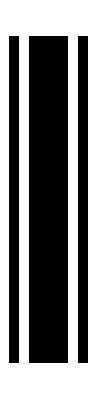
{-Graphics-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
out=Rest[Sort[ReadOutputFile[]]];
Length[out]
{AArrayPlot[rule, RandomInteger[k-1, 300]],ParallelMap[Labeled[AArrayPlot[rule, #, DecentRunLength[#, 30]], ClickToCopy[#, {rule,#}]]&,Sort[out[[;;UpTo[10]]]]]}
```

```mathematica
out=Rest[Sort[ReadOutputFile[]]];
Length[out]
outDeduped=FromDigits[#, k]&/@Union[Join@@ParallelTable[SplitSeparateSolutions2[CellularAutomaton[rule, {IntegerDigits[init, k], 0}, 1000][[-100;;]], rule], {init, out}]];
Length[outDeduped]
outDeduped2=DedupSame[Join@@ParallelMap[DetectPeriod[rule, #]&, outDeduped]][[All, "Original"]];
Length[outDeduped2]
ParallelMap[Labeled[AArrayPlot[rule, #, DecentRunLength[#, 300]], ClickToCopy[#]]&,Sort[RandomSample[outDeduped2, UpTo[250]]]]
ParallelMap[Labeled[AArrayPlot[rule, #, DecentRunLength[#, 300]], ClickToCopy[#]]&,Sort[RandomSample[out, UpTo[250]]]]
```

13

13

9

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}